```mathematica
SetDirectory[NotebookDirectory[]];
totData={Sample1Cooling=Import["D:\\Experiments\\Superconductivity_data_analysis\\Sample_1_Cooling.txt","Data"],Sample1Heating=Import["D:\\Experiments\\Superconductivity_data_analysis\\Sample_1_heating.txt","Data"],
Sample2Cooling=Import["D:\\Experiments\\Superconductivity_data_analysis\\Sample_2_cooling.txt","Data"],
Sample2Heating=Import["D:\\Experiments\\Superconductivity_data_analysis\\Sample_2_heating.txt","Data"],
Sample3Cooling=Import["D:\\Experiments\\Superconductivity_data_analysis\\Sample_3_cooling.txt","Data"],
Sample3Heating=Import["D:\\Experiments\\Superconductivity_data_analysis\\Sample_3_heating.txt","Data"],
Sample4Cooling=Import["D:\\Experiments\\Superconductivity_data_analysis\\Sample_4_cooling.txt","Data"],
Sample4Heating=Import["D:\\Experiments\\Superconductivity_data_analysis\\Sample_4_heating.txt","Data"]};
```

```mathematica
Sample1Cooling[[1]]
Sample3Cooling[[78]]
```

{293.5,100.218,0.5,0.05}

{294.986,130.317,0.5,0.065}

```mathematica
pltList=Table[Transpose[{totData[[i]][[All,1]],totData[[i]][[All,2]]}],{i,1,8}];
```

```mathematica
Show[ListLinePlot[{pltList[[1]],pltList[[2]],pltList[[5]][[78;;-1,All]],pltList[[6]]},PlotRange->All,PlotTheme->"Detailed",PlotLegends->{"Sample 1: Cooling", "Sample 1: Heating","Sample 3: Cooling","Sample 3: Heating"}],FrameLabel->{"Temperature (K)", "Resistance (mΩ)"}]
```

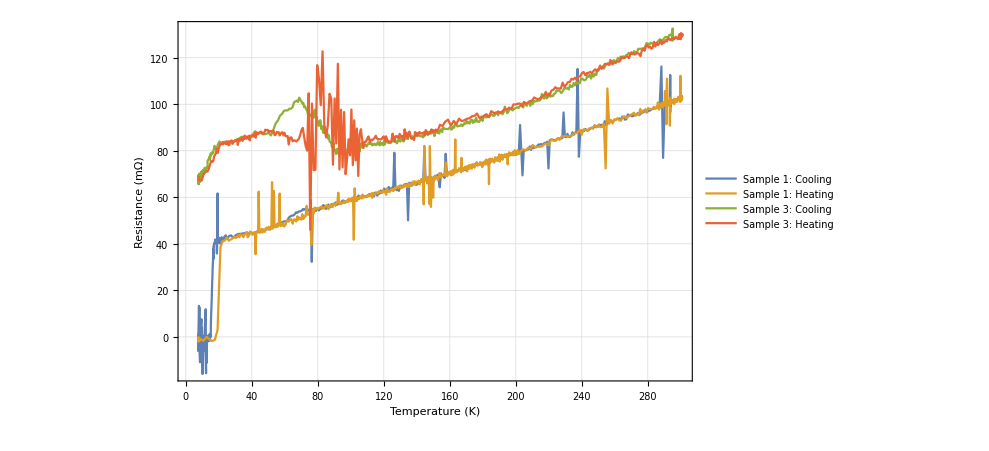

```mathematica
Show[ListLinePlot[{pltList[[4]]},PlotRange->All,PlotTheme->"Detailed",PlotLegends->{ "Sample 2: Heating"}],FrameLabel->{"Temperature (K)", "Resistance (mΩ)"}]
```

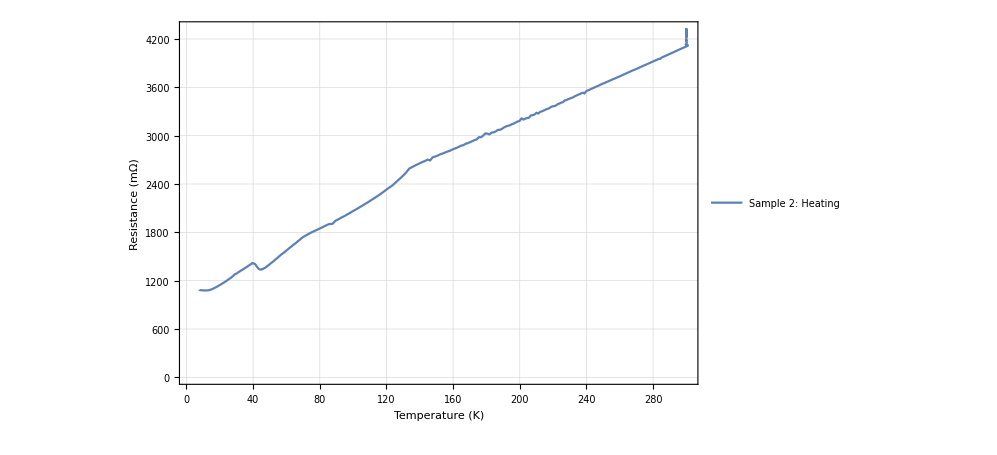

```mathematica
Length[pltList[[3]]]
```

601

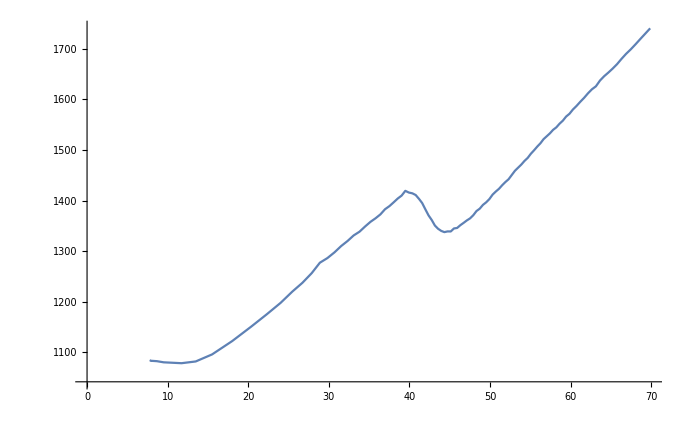

```mathematica
ListLinePlot[pltList[[4]][[1;;100,All]]]
```

```mathematica
340*10^(-3)*0.5(1.1/100+1.3/130)*10^(-1)
```

0.000357

```mathematica
%86*0.13*6.48
```

0.000300737

```mathematica
Show[ListPlot[{pltList[[2]][[1;;47,All]],pltList[[6]][[1;;80,All]]},PlotRange->All,PlotTheme->"Detailed",PlotLegends->{"Sample 1: Heating","Sample 3: Heating"}],Plot[{sample1fit[x],sample2fit[x]},{x,3,40},PlotLegends->{"21.22-22.34 tanh(24.69-1.22 x)","75.65-9.78 tanh(2.19-0.14 x)"}],FrameLabel->{"Temperature (K)", "Resistance (mΩ)"}]
```

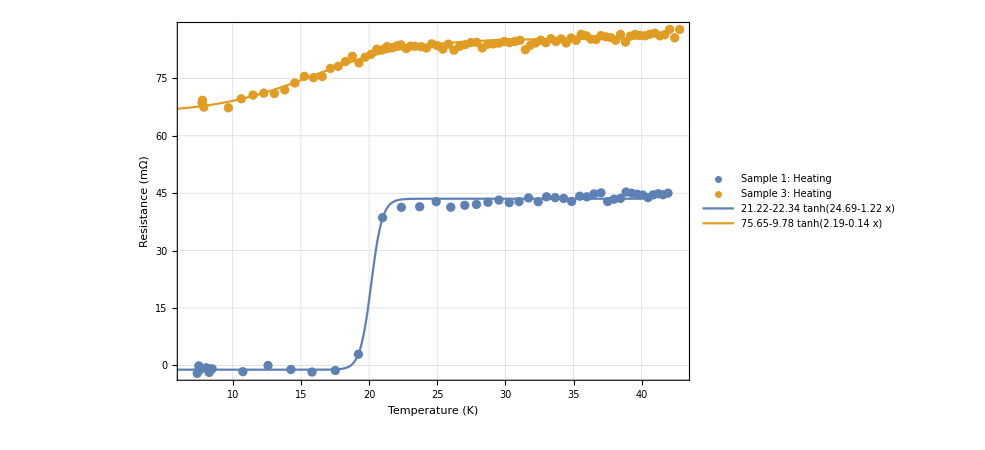

```mathematica
sample1fit=NonlinearModelFit[pltList[[2]][[1;;47,All]],a Tanh[b x+c]+d,{a,b,c,d},x]
sample2fit=NonlinearModelFit[pltList[[6]][[1;;80,All]],a Tanh[b x+c]+d,{a,b,c,d},x,Method->"Newton"]
```

FittedModel[21.223-22.3353 Tanh[24.6925-1.22514 x]]

FittedModel[75.6487-9.77889 Tanh[2.18932-0.13832 x]]

```mathematica
Solve[24.692459398920374-1.2251354346323597 x==0,x]
```

{{x→20.1549}}

```mathematica
Solve[2.1893170377407127-0.1383200433443373 x==0,x]
```

{{x→15.8279}}